```mathematica
(*https://www.twilio.com/blog/intro-to-markov-models-with-swift*)
```

```mathematica
rick = "Never gonna give you up
Never gonna let you down
Never gonna run around and desert you
Never gonna make you cry
Never gonna say goodbye
Never gonna tell a lie and hurt you";
```

```mathematica
rickSplit= StringSplit[rick]
```

{Never,gonna,give,you,up,Never,gonna,let,you,down,Never,gonna,run,around,and,desert,you,Never,gonna,make,you,cry,Never,gonna,say,goodbye,Never,gonna,tell,a,lie,and,hurt,you}

Histogram to represent weighted distributions

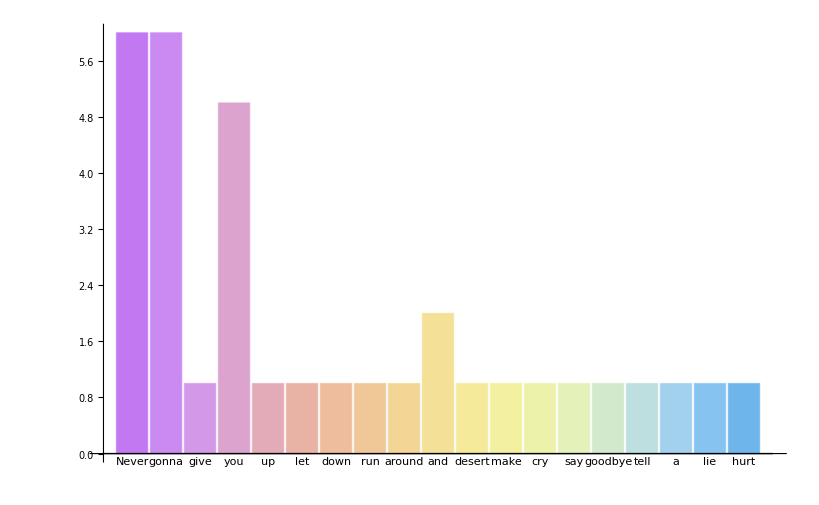

```mathematica
BarChart[#2,ChartLabels->#1, ChartStyle-> "Pastel"]&@@Transpose[Tally@rickSplit]
```

```mathematica
rickSentence=StringSplit[rick, "\n"];
```

```mathematica
states= Sort[Partition[rickSplit,2,1] //Counts,Greater]
```

<|{Never,gonna}→6,{hurt,you}→1,{and,hurt}→1,{lie,and}→1,{a,lie}→1,{tell,a}→1,{gonna,tell}→1,{goodbye,Never}→1,{say,goodbye}→1,{gonna,say}→1,{cry,Never}→1,{you,cry}→1,{make,you}→1,{gonna,make}→1,{you,Never}→1,{desert,you}→1,{and,desert}→1,{around,and}→1,{run,around}→1,{gonna,run}→1,{down,Never}→1,{you,down}→1,{let,you}→1,{gonna,let}→1,{up,Never}→1,{you,up}→1,{give,you}→1,{gonna,give}→1|>

```mathematica
data =ArrayComponents@states
```

{{1,2},{3,4},{3,5},{6,3},{7,8},{4,9},{10,8},{11,9},{12,11},{12,13},{12,14},{12,15},{12,16},{12,17},{18,8},{5,9},{13,9},{2,3},{14,9},{8,12},{8,12},{8,12},{8,12},{8,12},{8,12},{15,6},{16,18},{17,1},{19,8},{9,7},{9,10},{9,8},{9,19}}

```mathematica
states
```

{{a,lie},{and,desert},{and,hurt},{around,and},{cry,Never},{desert,you},{down,Never},{give,you},{gonna,give},{gonna,let},{gonna,make},{gonna,run},{gonna,say},{gonna,tell},{goodbye,Never},{hurt,you},{let,you},{lie,and},{make,you},{Never,gonna},{Never,gonna},{Never,gonna},{Never,gonna},{Never,gonna},{Never,gonna},{run,around},{say,goodbye},{tell,a},{up,Never},{you,cry},{you,down},{you,Never},{you,up}}

```mathematica
statesWRule=# /.List-> Rule&/@states
```

{a→lie,and→desert,and→hurt,around→and,cry→Never,desert→you,down→Never,give→you,gonna→give,gonna→let,gonna→make,gonna→run,gonna→say,gonna→tell,goodbye→Never,hurt→you,let→you,lie→and,make→you,Never→gonna,Never→gonna,Never→gonna,Never→gonna,Never→gonna,Never→gonna,run→around,say→goodbye,tell→a,up→Never,you→cry,you→down,you→Never,you→up}

```mathematica
Graph[statesWRule,GraphLayout->"LayeredDrawing"]
```

-Graphics-

```mathematica
Graph[statesWRule]
```

-Graphics-

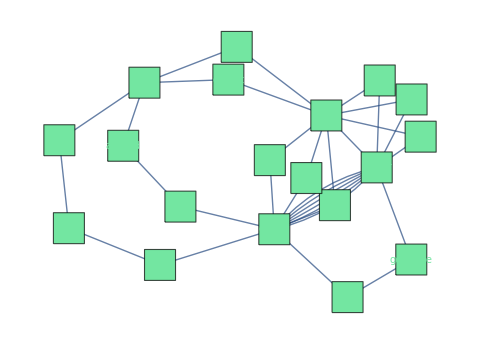

```mathematica
stateg=Graph[statesWRule, VertexShapeFunction->"Square",VertexSize->{.2,.2}, VertexLabels->Placed["Name",Center],VertexStyle->Hue[0.4,0.5,0.9],VertexLabelStyle->Directive[FontFamily->"Arial",10],ImageSize->480, EdgeShapeFunction->GraphElementData["ShortFilledArrow"]]
```

Removing duplicate edges-

```mathematica
EdgeList@SimpleGraph[stateg]
```

{a->lie,and->hurt,lie->and,tell->a,gonna->give,gonna->let,gonna->make,gonna->say,gonna->tell,and->desert,say->goodbye,you->down,you->up,desert->you,give->you,hurt->you,let->you,make->you,Never->gonna,down->Never,goodbye->Never,up->Never,you->Never,cry->Never,you->cry,around->and,run->around,gonna->run}

```mathematica
TableForm[Apply[List,%245,{1}]]
```

a | lie
and | hurt
lie | and
tell | a
gonna | give
gonna | let
gonna | make
gonna | say
gonna | tell
and | desert
say | goodbye
you | down
you | up
desert | you
give | you
hurt | you
let | you
make | you
Never | gonna
down | Never
goodbye | Never
up | Never
you | Never
cry | Never
you | cry
around | and
run | around
gonna | run

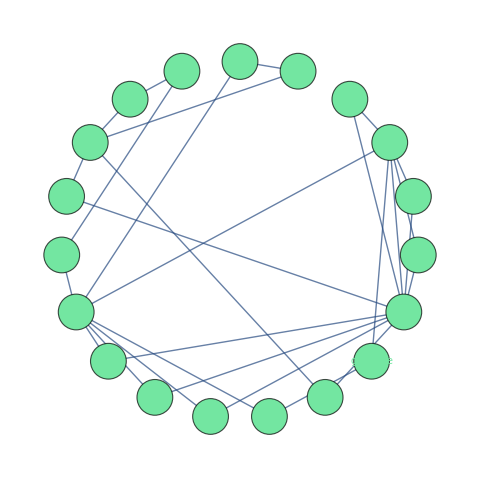

```mathematica
Graph[%245, VertexShapeFunction->"Circle",VertexSize->{.1,.1}, VertexLabels->Placed["Name",Center],VertexStyle->Hue[0.4,0.5,0.9],VertexLabelStyle->Directive[FontFamily->"Arial",10],ImageSize->480, EdgeShapeFunction->GraphElementData["ShortFilledArrow"], GraphLayout->"CircularEmbedding"]
```

```mathematica
AdjacencyMatrix[statesWRule]
```

SparseArray[<28>, {19, 19}]

```mathematica
MatrixForm[%221]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SimpleGraph[%224]
```

SimpleGraph::graph: A graph object is expected at position 1 in SimpleGraph[SparseArray[Automatic,{19,19},0,{1,{{0,1,2,4,5,6,7,8,9,13,14,15,21,22,23,24,25,26,27,28},{{2},{3},{4},{5},{9},{9},{3},{8},{12},{7},{8},{10},{19},{8},{9},{11},{13},{14},{15},{16},{17},{9},{9},{6},{18},{1},{8},{8}}},{1,1,1,1,1,1,1,1,6,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]].

SimpleGraph[SparseArray[<28>, {19, 19}]]

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/CrossTabulate.m"];
```

transition probability matrix

```mathematica
cmat=CrossTabulate[states];
MatrixForm[cmat]
```

( | a | and | around | cry | desert | down | give | gonna | goodbye | hurt | let | lie | make | run | say | tell | up | you
a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
and | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
around | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
desert | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
give | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
gonna | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0
hurt | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
let | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
lie | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
make | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
Never | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
run | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
say | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
tell | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
you | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
cmat["SparseMatrix"]
```

SparseArray[<23>, {15, 18}]

```mathematica
cmat["SparseMatrix"]=cmat["SparseMatrix"]/Total[cmat["SparseMatrix"],{2}];
MatrixForm[cmat]
```

( | a | and | around | cry | desert | down | give | gonna | goodbye | hurt | let | lie | make | run | say | tell | up | you
a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
and | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
around | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
desert | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
give | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
gonna | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0
hurt | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
let | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
lie | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
make | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
Never | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
run | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
say | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
tell | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
you | 0 | 0 | 0 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0)

```mathematica
ArrayRules[cmat["SparseMatrix"]]
```

{{1,12}→1,{2,5}→1/2,{2,10}→1/2,{3,2}→1,{4,18}→1,{5,18}→1,{6,7}→1/6,{6,11}→1/6,{6,13}→1/6,{6,14}→1/6,{6,15}→1/6,{6,16}→1/6,{7,18}→1,{8,18}→1,{9,2}→1,{10,18}→1,{11,8}→1,{12,3}→1,{13,9}→1,{14,1}→1,{15,4}→1/3,{15,6}→1/3,{15,17}→1/3,{_,_}→0}

```mathematica
cmat
```

<|SparseMatrix→SparseArray[<23>, {15, 18}],RowNames→{a,and,around,desert,give,gonna,hurt,let,lie,make,Never,run,say,tell,you},ColumnNames→{a,and,around,cry,desert,down,give,gonna,goodbye,hurt,let,lie,make,run,say,tell,up,you}|>

```mathematica
ArrayRules@cmat["SparseMatrix"]
```

{{1,12}→1,{2,5}→1/2,{2,10}→1/2,{3,2}→1,{4,18}→1,{5,18}→1,{6,7}→1/6,{6,11}→1/6,{6,13}→1/6,{6,14}→1/6,{6,15}→1/6,{6,16}→1/6,{7,18}→1,{8,18}→1,{9,2}→1,{10,18}→1,{11,8}→1,{12,3}→1,{13,9}→1,{14,1}→1,{15,4}→1/3,{15,6}→1/3,{15,17}→1/3,{_,_}→0}

```mathematica
Graph[cmat["SparseMatrix"]]
```

Graph[SparseArray[<23>, {15, 18}]]